# Light in the cup

By GHe(σ)

## Question：

在一个圆柱杯中，在杯壁有一光源向四周发出光线，光线遇到杯壁发生反射，现只考虑单次反射。在光线交汇的地方，光亮的强度产生叠加，于是比周围其他的点更亮，即反射光线的包络线会比其他地方更亮。现求观察到的曲线的形状，即求反射光线的包络线

## Answer：

现在根据题意，画出示意图。设圆的半径为R，圆心坐标为 (0,0)，点光源为A点，反射点为B点，如图：

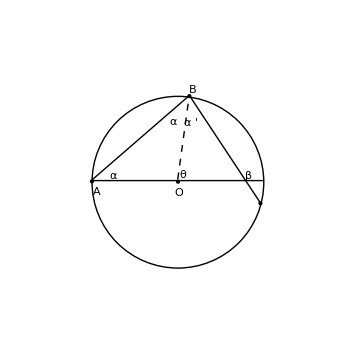

由反射关系可知 α=α'
由图可知 θ=2α，β=α'+θ=3α=3/2 θ，点B的坐标为 (R cos(θ),R sin(θ))
反射光线的斜率 k=tan(β)=tan(3/2 θ)，反射光线经过B点，可以解出反射光线 y=kx+b,其中

k=tan(3/2 θ)
 b=R sin(θ)-R cos(θ)tan(3/2 θ)

### Solution Ⅰ

现取一条靠近 y=kx+b 的另一反射光线 y=(k+dk)x+(b+db)，联立可得这两条光线的交点坐标：

x=-db/dk=-(b'(θ))/(k'(θ))
y=(b dk - k db)/dk=(b (θ)k'(θ)-k(θ)b'(θ))/(k'(θ))

带入前文得出的 k，b 的表达式：

```mathematica
k[t_]:=Tan[3/2 t];
b[t_] :=R Sin[t]-R Cos[t] Tan[(3 t)/2];
X=TrigReduce[-D[b[t],t]/D[k[t],t]] // Simplify
Y=TrigReduce[(b[t]*D[k[t],t]-k[t]*D[b[t],t])/D[k[t],t]] //Simplify
```

-1/3 R (-2 Cos[t]+Cos[2 t])

-2/3 R (-1+Cos[t]) Sin[t]

因此，我们可以得到该包络线的参数方程，如下（t为参数）：

x=1/3 R [2 cos(t)-cos(2 t)]
y=1/3 R [2sin(t)-sin(2 t)]

### Solution Ⅱ

包络线满足下面两条方程：

F(x,y,t)=0
(∂F)/(∂t)=0

由前文有：F(x,y,t) = tan(3/2)x - y + R sin(t) - R cos(t) tan(3/2 t) = 0

求偏导：

```mathematica
F=Tan[3/2 t]x-y+R Sin[t]-R Cos[t] Tan[(3 t)/2];
D[F,t]
```

R Cos[t]+3/2 x Sec[(3 t)/2]^2-3/2 R Cos[t] Sec[(3 t)/2]^2+R Sin[t] Tan[(3 t)/2]

(∂F)/(∂t)=R cos(t)+3/2 x sec(3/2 t)^2-3/2 R cos(t)sec(3/2 t)^2+R sin(t) tan(3/2 t)

联立解方程：

```mathematica
TrigReduce[Solve[{F==0,D[F,t]==0},{x,y},Reals]] //Simplify
```

{{x→-1/3 R (-2 Cos[t]+Cos[2 t]),y→-2/3 R (-1+Cos[t]) Sin[t]}}

因此，我们可以得到该包络线的参数方程，如下（t为参数）：

x=1/3 R [2 cos(t)-cos(2 t)]
y=1/3 R [2sin(t)-sin(2 t)]

### 绘图

根据参数方程，我们便可以绘制出该包络线图像：

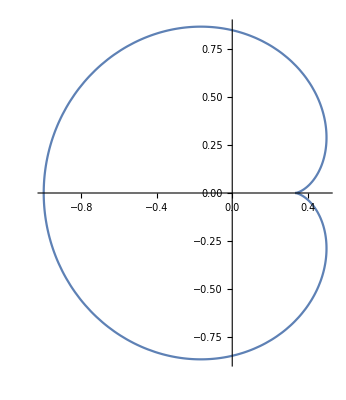

```mathematica
X=X /.R->1;
Y=Y /.R->1;
ParametricPlot[{X,Y},{t,0,2π}]
```

可见包络线为心形线，即在杯子中能观察到的曲线是心形线。

我们可以绘制不同θ下的反射光线，以验证其包络线是否为心形线

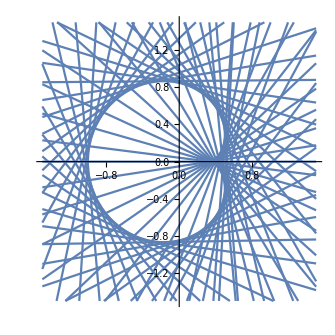

```mathematica
Plot[Table[Tan[3/2 t]*x+Sin[t]-Cos[t] Tan[(3 t)/2],{t,0,2π,0.1}],{x,-1.5,1.5},PlotRange->{-1.5,1.5},AspectRatio->1]
```

可见我们所求确为要求的包络线。

### 现实中的图像

```mathematica
-Graphics--Graphics-
```

图一在日常生活中当光源位置合适时很容易观察到。
图二由于杯壁反射率较高，且光源较亮，两次反射仍旧有较高的亮度，故可以看见两条心形线。但在一般情况下，第二次反射的亮度太低，难以观察到，故一般情况下只能看见一条心形线。